```mathematica
i=Import["C:\\fpgithub\\0908-LHWZ\\data\\01_Uran_Zaehlrohrcharakteristik_1000-4000-100.txt","Table"];
```

```mathematica
i
```

{{1000000,26440},{1100000,26860},{1200000,27960},{1300000,28340},{1400000,28880},{1500000,26860},{1600000,29400},{1700000,30040},{1800000,30280},{1900000,31120},{2000000,34740},{2100000,43260},{2200000,59240},{2300000,87720},{2400000,140020},{2500000,240820},{2600000,403860},{2700000,599460},{2800000,716180},{2900000,769680},{3000000,816140},{3100000,828200},{3200000,836760},{3300000,859120},{3400000,878860},{3500000,952020},{3600000,1077080},{3700000,1380220},{3800000,1839900},{3900000,2308700},{4000000,2768040}}

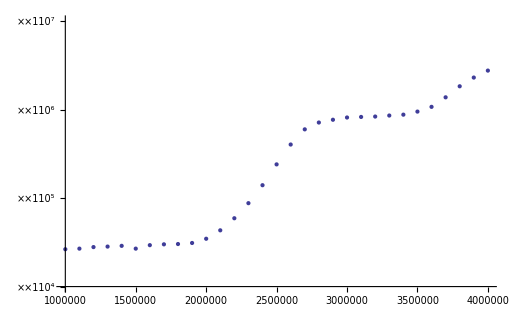

```mathematica
ListLogPlot[i,PlotRange->{10^4,10^7}]
```